```mathematica
data = Import["C:\\Users\\Alexey\\Downloads\\Imitator.csv", "Table"]
```

```mathematica
Dimensions[data]
```

{2401,15}

```mathematica
A=Array[a, 2401]
```

```mathematica
Do[a[k]=data[[k,6]], {k, 1, 2401}]
```

```mathematica
td=TemporalData[A]
```

TemporalData[…]

```mathematica
tsm=TimeSeriesModelFit[td, "SARIMA"]
```

TimeSeriesModel[…]

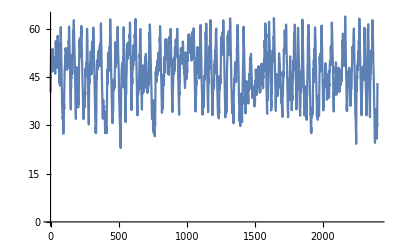

```mathematica
ListLinePlot[td, PlotRange->All]
```

```mathematica
TimeSeriesForecast[tsm, {20}]
```

TemporalData[…]

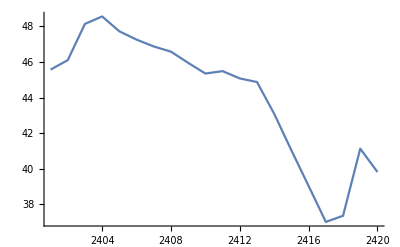

```mathematica
ListLinePlot[%237]
```

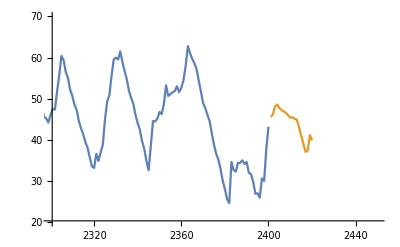

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{20}]}, PlotRange->{{2300, 2450}, {20,70}}]
```

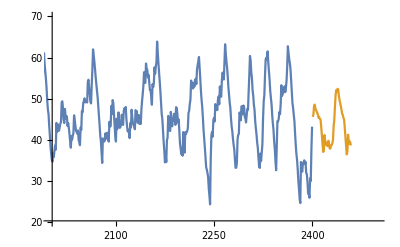

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{60}]}, PlotRange->{{2000, 2500}, {20,70}}]
```

```mathematica
Samp=Array[s, 350]
```

```mathematica
Do[s[k]=A[[2401-350+k]], {k,1, 350}]
```

```mathematica
TDSamp=TemporalData[Samp]
```

TemporalData[…]

```mathematica
TimeSeriesModelFit[TDSamp, "SARIMA"]
```

TimeSeriesModel[…]

```mathematica
Normal[%118]
```

ARMAProcess[2.6373,{0.942702},{0.0926773},6.22752]

```mathematica
WeakStationarity[ARMAProcess[2.6372951723447366,{0.94270206991412},{0.09267728353333188},6.227519759970664]]
```

True

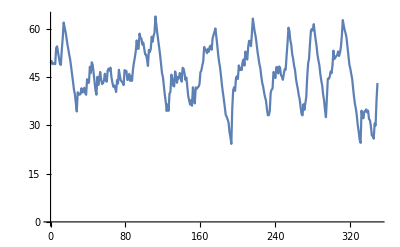

```mathematica
ListLinePlot[TDSamp]
```

```mathematica
TSamp=TimeSeriesModelFit[TDSamp, "SARIMA"]
```

TimeSeriesModel[…]

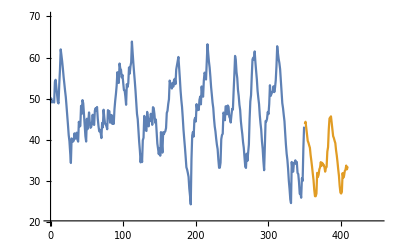

```mathematica
ListLinePlot[{TSamp["TemporalData"],TimeSeriesForecast[TSamp,{60}]}, PlotRange->{{0, 450}, {20,70}}]
```

```mathematica
Dimensions[data]
```

{2401,15}

```mathematica
T=Array[t, 2401]
```

```mathematica
Do[t[i]=i, {i,1, 2401}]
```

```mathematica
Dat=Array[d, {2401, 10}]
```

```mathematica
Do[d[i,j]=data[[i,5+j]], {i, 1, 2401}, {j,1, 10}]
```

```mathematica
TimeSeriesModelFit[Dat]
```

TimeSeriesModel[…]

```mathematica
Normal[%142]
```

MAProcess[46.197,{},25.4099]

```mathematica
TSM=%142
```

TimeSeriesModel[…]

```mathematica
Do[Subscript[V, k]=Array[Subscript[v, k], 2401], {k,1,10}]
```

```mathematica
Do[Subscript[v, j][i]=data[[i,5+j]], {i, 1, 2401}, {j,1, 10}]
```

```mathematica
TD=TemporalData[{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],Subscript[v, 4],Subscript[v, 5],Subscript[v, 6],Subscript[v, 7],Subscript[v, 8],Subscript[v, 9],Subscript[v, 10]},T]
```

```mathematica
TD=TemporalData[{Subscript[V, 1], Subscript[V, 2]}, {T}]
```

TemporalData[…]

```mathematica
TSM=TimeSeriesModelFit[TD, "SARIMA"]
```

TimeSeriesModel[…]

```mathematica
TimeSeriesForecast[TSM,{60}]
```

TemporalData[…]

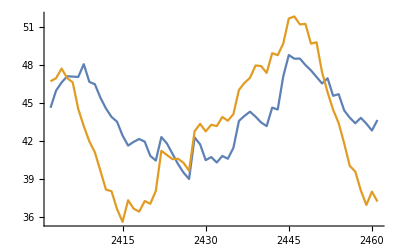

```mathematica
ListLinePlot[%242]
```

```mathematica
TDFull=TemporalData[{Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],Subscript[V, 7],Subscript[V, 8],Subscript[V, 9],Subscript[V, 10]},{T}]
```

TemporalData[…]

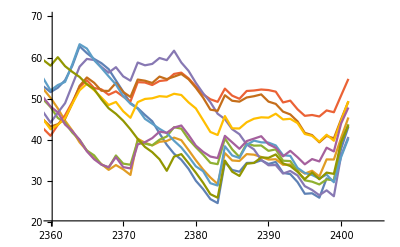

```mathematica
ListLinePlot[TDFull, PlotRange->{{2360,2405},{20,70}}]
```

```mathematica
TSMFull=TimeSeriesModelFit[TDFull, "SARIMA"]
```

TimeSeriesModel[…]

TimeSeriesModel[…]

```mathematica
ListLinePlot[{TDFull,TimeSeriesForecast[TSMFull,{60}]}, PlotRange->{{2380, 2460}, {20,70}}, Joined->True]
```

-Graphics-

```mathematica
TimeSeriesForecast[TSMFull,{60}]
```

TemporalData[…]

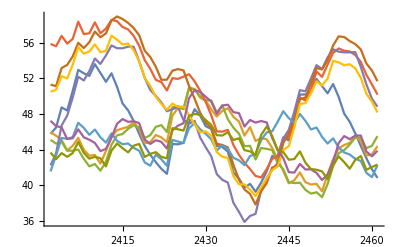

```mathematica
ListLinePlot[%245]
```

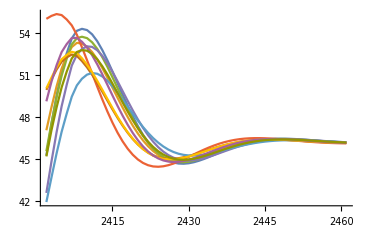

```mathematica
ListLinePlot[%210]
```

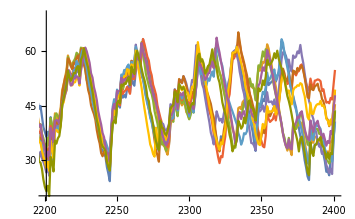
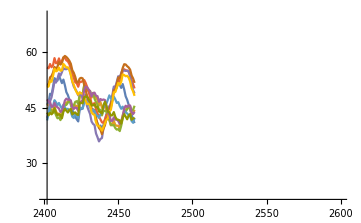

```mathematica
{ListLinePlot[TDFull, PlotRange->{{2200,2401},{20,70}}],ListLinePlot[%245,PlotRange->{{2401,2600},{20,70}}]}
```